```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]=Sin[Pi x/2]*(1-Exp[-2Pi x]);
f'[1.]
```

0.0117335

```mathematica
nosim=Import["hnosim.txt","Table"];
sim=Import["hsim.txt","Table"];
richard=Import["hri.txt","Table"];
realnosim=Import["realhnosim.txt","Table"];
realsim=Import["realhnosim.txt","Table"];
realrichard=Import["realhnosim.txt","Table"];
```

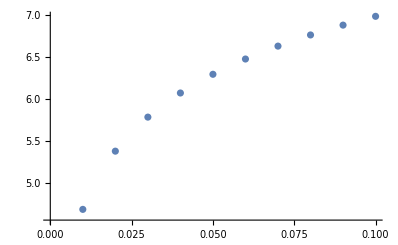

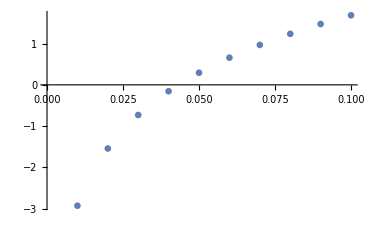

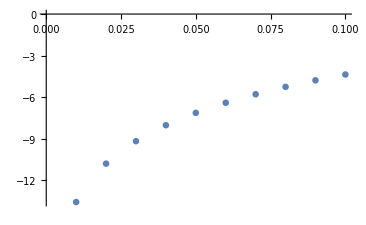

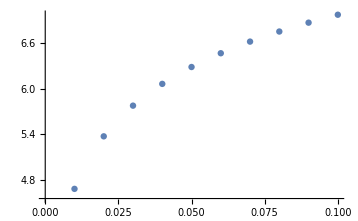

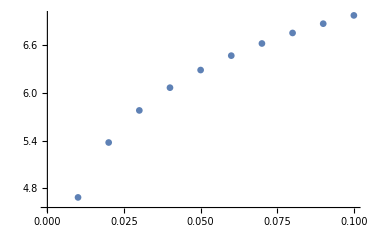

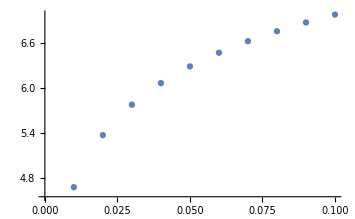

```mathematica
ListPlot[nosim]
ListPlot[sim]
ListPlot[richard]
ListPlot[realnosim]
ListPlot[realsim]
ListPlot[realrichard]
```

Como esperamos, todos los logarítmos de los errores van como log(h), ya que sabemos que el error en nuestras aproximaciones debería ir como o(h^n), de manera que su logarítmo debería ir como o(n log(h)) = o(log(h)). Es importante notar que en todos los gráficos, el error en aquel que se ha utilizado simple precisión es bastante más grande que en los que se há utilizado presición simple.